### Speed of a Random walk

```mathematica
L=11;
```

```mathematica
M=Table[If[Abs[i-j]<= 1, If[i==j, If[i==1 || i==L, -1,-2], 1], 0],{i, 1, L}, {j, 1, L}]
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

{{-1,1,0,0,0,0,0,0,0,0,0},{1,-2,1,0,0,0,0,0,0,0,0},{0,1,-2,1,0,0,0,0,0,0,0},{0,0,1,-2,1,0,0,0,0,0,0},{0,0,0,1,-2,1,0,0,0,0,0},{0,0,0,0,1,-2,1,0,0,0,0},{0,0,0,0,0,1,-2,1,0,0,0},{0,0,0,0,0,0,1,-2,1,0,0},{0,0,0,0,0,0,0,1,-2,1,0},{0,0,0,0,0,0,0,0,1,-2,1},{0,0,0,0,0,0,0,0,0,1,-1}}

```mathematica
Prob[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[Val[[k]] t], {k, 1, L}]
```

```mathematica
Prob[0]
```

{2.77556×10^-17,-2.77556×10^-17,2.77556×10^-17,2.77556×10^-17,5.55112×10^-17,1.,1.66533×10^-16,8.32667×10^-17,8.32667×10^-17,8.32667×10^-17,0.}

```mathematica
plot =Flatten[Table[{k, t, Prob[t][[k]]}, {k ,1, L}, {t, 0, 5, 1}],1];
```

```mathematica
ListPlot3D[plot, PlotRange->All]
```

-Graphics3D-

```mathematica
Eval[t_]:= Sum[k Prob[t][[k]], {k, 1, L}];
```

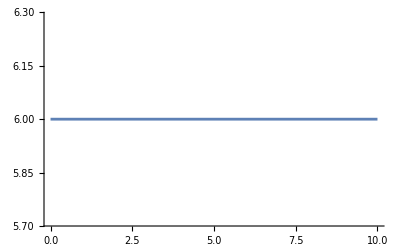

```mathematica
Plot[Eval[t], {t, 0, 10}]
```

```mathematica
SD[t_]:= (Sum[k^2 Prob[t][[k]], {k, 1, L}] - Eval[t]^2)^(1/2);
```

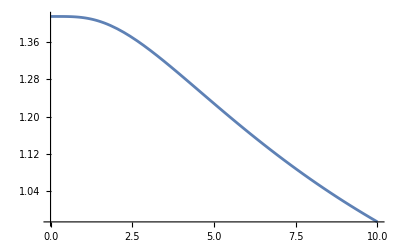

```mathematica
Plot[SD[t]/t^(1/2), {t, 0, 10}, PlotRange->Full]
```

```mathematica
N[√2]
```

1.41421

### Speed of a Random walk

```mathematica
L=21;
J=1;
```

```mathematica
M=Table[If[Abs[i-j]<= 1, If[i==j, If[i==1 || i==L, -J,-2 J], J], 0],{i, 1, L}, {j, 1, L}];
MatrixForm[M]
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

(-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1)

```mathematica
Prob[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[Val[[k]] t], {k, 1, L}]
```

```mathematica
Prob[0]//Round
```

{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
plot =Flatten[Table[{k, t, Prob[t][[k]]}, {k ,1, L}, {t, 0, 20, 1}],1];
```

```mathematica
ListPlot3D[plot, PlotRange->All]
```

-Graphics3D-

```mathematica
Eval[t_]:= Sum[k Prob[t][[k]], {k, 1, L}];
```

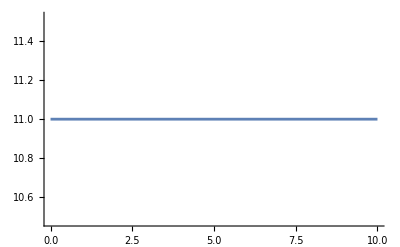

```mathematica
Plot[Eval[t], {t, 0, 10}]
```

```mathematica
SD[t_]:= (Sum[k^2 Prob[t][[k]], {k, 1, L}] - Eval[t]^2)^(1/2);
```

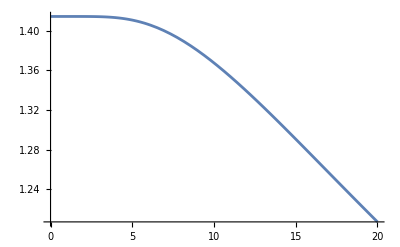

```mathematica
Plot[SD[t]/t^(1/2), {t, 0, 20}, PlotRange->Full]
```

```mathematica
N[√(2J)]
```

1.41421

### Speed of a Random walk

```mathematica
L=15;
J=1/10;
```

```mathematica
M =({{-1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, -1-J, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1/J, -1-1/J, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -1-1/J, 1/J, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J, -1-J, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, -1-J, J, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1/J, -1-1/J, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -1-1/J, 1/J, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, -J-1, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -1}});
```

```mathematica
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

```mathematica
Prob[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[Val[[k]] t], {k, 1, L}]
```

```mathematica
Prob[0]//Round
```

{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}

```mathematica
plot =Flatten[Table[{k, t, Prob[t][[k]]}, {k ,1, L}, {t, 0, 500, 1}],1];
```

General::munfl: 1.31198×10^-290 1.1826×10^-19 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.60203×10^-295 1.1826×10^-19 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.56445×10^-290 2.55624×10^-20 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
ListPlot3D[plot, PlotRange->All]
```

-Graphics3D-

```mathematica
Eval[t_]:= Sum[k Prob[t][[k]], {k, 1, L}];
```

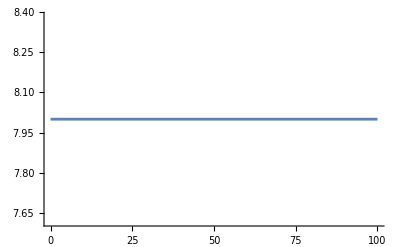

```mathematica
Plot[Eval[t], {t, 0, 100}]
```

```mathematica
SD[t_]:= (Sum[k^2 Prob[t][[k]], {k, 1, L}] - Eval[t]^2)^(1/2);
```

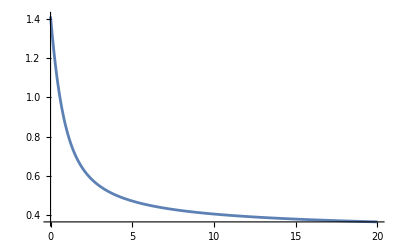

```mathematica
plotL15T= Plot[SD[t]/t^(1/2), {t, 0, 20}, PlotRange->Full]
```

```mathematica
N[√2]
```

1.41421

### Speed of a Random walk

```mathematica
L=3;
J=1;
```

```mathematica
M=Table[If[Abs[i-j]<= 1, If[i==j, If[i==1 || i==L, -J,-2 J], J], 0],{i, 1, L}, {j, 1, L}];
MatrixForm[M]
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

(-1 | 1 | 0
1 | -2 | 1
0 | 1 | -1)

```mathematica
Prob[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[Val[[k]] t], {k, 1, L}]
```

```mathematica
Prob[0]//Round
```

{0,1,0}

```mathematica
plot =Flatten[Table[{k, t, Prob[t][[k]]}, {k ,1, L}, {t, 0, 20, 1}],1];
```

```mathematica
ListPlot3D[plot, PlotRange->All]
```

-Graphics3D-

```mathematica
Eval[t_]:= Sum[k Prob[t][[k]], {k, 1, L}];
```

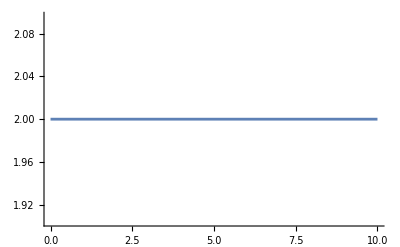

```mathematica
Plot[Eval[t], {t, 0, 10}]
```

```mathematica
SD[t_]:= (Sum[k^2 Prob[t][[k]], {k, 1, L}] - Eval[t]^2)^(1/2);
```

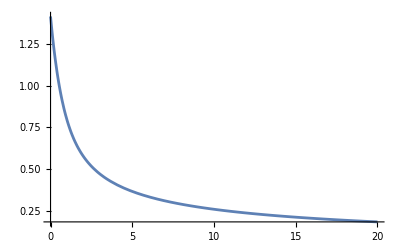

```mathematica
plotL3 = Plot[SD[t]/t^(1/2), {t, 0, 20}, PlotRange->Full]
```

```mathematica
N[√(2J)]
```

1.41421

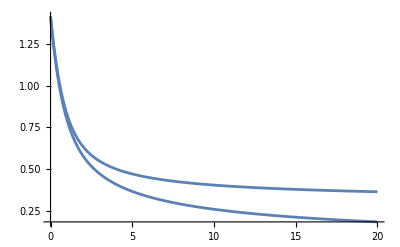

```mathematica
Show[plotL3, plotL15T]
```

### Mixing time

The limiting distribution is proportional to the vector
(1,1,1, J^2, J^2, J^2, 1, 1, 1, J^2, J^2, J^2, 1, 1, 1)
Below we determine the mixing time as a function of J by trying different values of J and fitting the data.

```mathematica
Points= {};
```

#### J=1/10

```mathematica
L=15;
J=1/10;
```

```mathematica
M =({{-1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, -1-J, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1/J, -1-1/J, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -1-1/J, 1/J, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J, -1-J, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, -1-J, J, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1/J, -1-1/J, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -1-1/J, 1/J, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, -J-1, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -1}});
```

```mathematica
Val = Eigenvalues[M]//N;
AppendTo[Points,{J,(SortBy[-Val, Re][[2]])^-1}]
```

{{1/10,667.246}}

#### J=1/5

```mathematica
L=15;
J=1/5;
```

```mathematica
M =({{-1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, -1-J, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1/J, -1-1/J, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -1-1/J, 1/J, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J, -1-J, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, -1-J, J, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1/J, -1-1/J, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -1-1/J, 1/J, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, -J-1, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -1}});
```

```mathematica
Val = Eigenvalues[M]//N;
AppendTo[Points,{J,(SortBy[-Val, Re][[2]])^-1}]
```

{{1/10,667.246},{1/5,187.383}}

#### J=1/20

```mathematica
L=15;
J=1/20;
```

```mathematica
M =({{-1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, -1-J, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1/J, -1-1/J, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -1-1/J, 1/J, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J, -1-J, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, -1-J, J, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1/J, -1-1/J, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -1-1/J, 1/J, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, -J-1, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -1}});
```

```mathematica
Val = Eigenvalues[M]//N;
AppendTo[Points,{J,(SortBy[-Val, Re][[2]])^-1}]
```

{{1/10,667.246},{1/5,187.383},{1/20,2527.2}}

#### J=1/7

```mathematica
L=15;
J=1/7;
```

```mathematica
M =({{-1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, -1-J, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1/J, -1-1/J, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -1-1/J, 1/J, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J, -1-J, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, -1-J, J, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1/J, -1-1/J, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -1-1/J, 1/J, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, -J-1, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -1}});
```

```mathematica
Val = Eigenvalues[M]//N;
AppendTo[Points,{J,(SortBy[-Val, Re][[2]])^-1}]
```

{{1/10,667.246},{1/5,187.383},{1/20,2527.2},{1/7,343.297}}

#### J=1/15

```mathematica
L=15;
J=1/15;
```

```mathematica
M =({{-1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, -1-J, J, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1/J, -1-1/J, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -1-1/J, 1/J, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, J, -1-J, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, -1-J, J, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1/J, -1-1/J, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -1-1/J, 1/J, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, J, -J-1, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -2, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -1}});
```

```mathematica
Val = Eigenvalues[M]//N;
AppendTo[Points,{J,(SortBy[-Val, Re][[2]])^-1}]
```

{{1/10,667.246},{1/5,187.383},{1/20,2527.2},{1/7,343.297},{1/15,1447.21}}

```mathematica
Points = SortBy[Points, First]
```

{{1/20,2527.2},{1/15,1447.21},{1/10,667.246},{1/7,343.297},{1/5,187.383}}

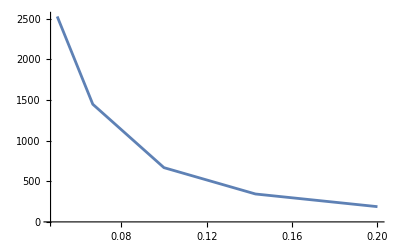

```mathematica
ListPlot[Points, Joined->True]
```

| Estimate | Standard Error | t-Statistic | P-Value
a1 | 2.19244 | 0.0350161 | 62.6122 | 8.97625×10^-6
b1 | -1.87904 | 0.0148005 | -126.958 | 1.07744×10^-6

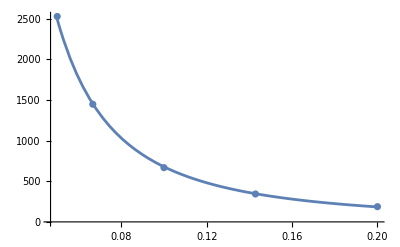

```mathematica
Ylog={Log[#[[1]]],Log[#[[2]]]}&/@Points;
nlm1=NonlinearModelFit[Ylog,a1+b1 x,{a1,b1},x];
nlm1["ParameterTable"]
Show[ListPlot[Points],Plot[Exp[nlm1[Log[x]]],{x,0.05,.2}]]
```

```mathematica
Exp[2.192438260327191]
```

8.95703

```mathematica
1.8790445891994991
```

We seem to obtain a power law
mixing time = (8.95703)J^-1.879